```mathematica
NotebookEvaluate["/home/chris/Programming/GPU/opencl3/build.wl"]
GPUStructureSearch[{20, {2, 1}, 2}, 0, 1000000]
```

{151,187,189,221,635,889,15903,125231,595703,610999,624623}

## Run 1

```mathematica
interestingRules={{3273447016,2,2},{3031436724,2,2}, {2079236760,2,2}, {3344875112,2,2}, {1514046372,2,2}, {2557749156,2,2} };
```

```mathematica
interestingResults=Table[rule->GPUStructureSearch[rule, 0, 1000000000], {rule, interestingRules}];
```

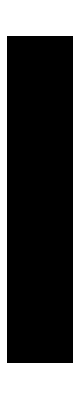
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
Column[ParallelTable[With[{rule=res[[1]]},{k=AnalyzeRule[rule]["Colors"]},Pane[{
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]], ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, 200]], ClickToCopy[init]]
, {init, res[[2, ;;UpTo[50]]]}], Spacer[1]]
}, 100000]], {res, interestingResults}]]
```

## Run 2

```mathematica
interestingRules={{2203608104,2,2}, {2761300852,2,2}, {1744748136,2,2}, {2748069448,2,2}, {3312889384,2,2}};
```

```mathematica
interestingResults=Table[rule->GPUStructureSearch[rule, 0, 1000000000, 120], {rule, interestingRules}];
```

```mathematica
interestingResults=Select[interestingResults, #[[2]]=!=$TimedOut&];
```

```mathematica
Column[ParallelTable[With[{rule=res[[1]]},{k=AnalyzeRule[rule]["Colors"]},Pane[{
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]], ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, 200]], ClickToCopy[init]]
, {init, res[[2, ;;UpTo[50]]]}], Spacer[1]]
}, 100000]], {res, interestingResults}]]
```

{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics-}

## Run 3

```mathematica
mildlyInterestingRules={{4038252832125,3,1},{157378344183,3,1}, {315063957102,3,1}, {417272523036,3,1}, {499889044356,3,1}, {532752959250,3,1}, {1253064233616,3,1}, {1106671480962,3,1}, {1050097186971,3,1}, {1036984688376,3,1}, {875716455717,3,1}, {1384508549211,3,1}, {1420458055773,3,1}, {1439484372981,3,1}, {1440660571524,3,1}, {1450654416753,3,1}, {1467399317553,3,1},  {1527732453375,3,1}, {1698397792845,3,1}, {1792956575223,3,1}, {1933164805722,3,1}, {2006767696968,3,1}, {2016801282741,3,1}, {2156321551974,3,1}, {2171809003401,3,1}, {2321701470540,3,1}, {2286903243951,3,1}, {2229561681774,3,1}, {2506488287697,3,1}, {3015295680177,3,1}, {3205622170005,3,1}, {3330333028152,3,1},  {4325130788595,3,1}, {4421912889159,3,1}, {4706695886958,3,1}, {5018159827026,3,1}, {5287229787156,3,1}, {5425558869390,3,1}, {5726559850350,3,1}, {5988206843826,3,1}, {6011373183351,3,1}, {6969584474595,3,1}};
```

#### Glider Guns etc.

```mathematica
interestingRules={{1467399317553,3,1},  {5726559850350,3,1},{5287229787156,3,1}};
```

```mathematica
interestingResults=Table[rule->GPUStructureSearch[rule, 0,1000000, 120], {rule, interestingRules}];
```

```mathematica
Length[interestingResults]
interestingResults=Select[interestingResults, #[[2]]=!=$TimedOut&];
Length[interestingResults]
```

3

3

```mathematica
Column[ParallelTable[With[{rule=res[[1]]},{k=AnalyzeRule[rule]["Colors"]},Pane[{
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]], ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, 500]], ClickToCopy[init]]
, {init, res[[2, ;;UpTo[50]]]}], Spacer[1]]
}, 100000]], {res, interestingResults}]]
```

{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
Row[ArrayPlot[CellularAutomaton[{5287229787156,3,1}, {IntegerDigits[#, 3], 0}, 3000], ImageSize->{Automatic, 300}]&/@{17844584418643230868, 12011, 189070}]
```

-Graphics--Graphics--Graphics-

#### Interesting Long-Run

```mathematica
interestingRules={{875716455717,3,1}, {1527732453375,3,1}, {1698397792845,3,1}, {2016801282741,3,1},  {2286903243951,3,1},  {2506488287697,3,1}, {3015295680177,3,1},{3330333028152,3,1},  {4325130788595,3,1}, {4421912889159,3,1}, {5018159827026,3,1}, {5988206843826,3,1}, {6011373183351,3,1}};
```

```mathematica
interestingResults=Table[rule->GPUStructureSearch[rule, 0, 1000000000, 300], {rule, interestingRules}];
```

```mathematica
Length[interestingResults]
interestingResults=Select[interestingResults, #[[2]]=!=$TimedOut&];
Length[interestingResults]
```

13

13

```mathematica
Clear[DecentRunLength]
DecentRunLength[rule_, init_, k_, default_:400,dieoutcheck_:3000]:=With[
{p=Length[FindTransientRepeat[StripZeros/@CellularAutomaton[rule, {IntegerDigits[init, k], 0}, 100], 2][[2]]]}, If[p!=0, 40+3*p, 
If[
Total[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, {{{dieoutcheck}}}]]==0,
5+Round[1.2*Length[
StripZeros[Total[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, dieoutcheck], {2}]]]],
default
]]]
```

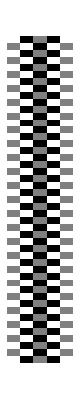
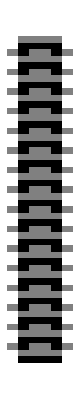
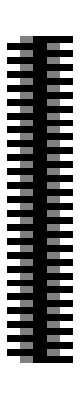
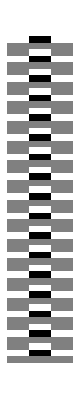
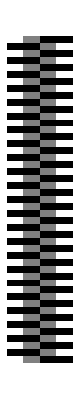
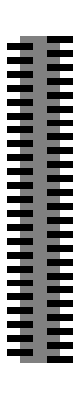
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
Column[ParallelTable[With[{rule=res[[1]]},{k=AnalyzeRule[rule]["Colors"]},Pane[{
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]], ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, DecentRunLength[rule, init, k]]], ClickToCopy[init]]
, {init, res[[2, ;;UpTo[50]]]}], Spacer[1]]
}, 100000]], {res, interestingResults}]]
```